```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
(*Needs["Screening`",NotebookDirectory[]<>"../packages/Screening.wl"]*)
```

#### Cross-section Interpolation Syntax Tutorial

This subsection is meant as a tutorial for accessing the data stored in the*σDict*. dat files. 

The cross-sections (all of which scale as κ^2, so we have set κ=1 and can rescale as needed) are separated into either *σDicte.dat or *σDictNuc.dat files depending on whether they are nuclear or electronic cross-sections. The electronic and nuclear files for Iron are loaded as

```mathematica
FeσDictNuc=ReadIt[NotebookDirectory[]<>"FeσDictNuc"];
FeσDicte=ReadIt[NotebookDirectory[]<>"FeσDicte"];
```

Each file is stored as a table, each entry of which is for a particular mass (currently scanned over MeV to PeV in factors of 10).  For example to look at the Iron cross-sections with a 1 GeV aDM probe, we access the 4th entry of the FeσDict* tables.

```mathematica
Position[Round@Log10["mχ"(("JpereV")/("c")^2)^-1]/.FeσDictNuc/.SIConstRepl,Round@9][[1]]
Union[Position[Round@Log10["mχ"(("JpereV")/("c")^2)^-1]/.FeσDicte/.SIConstRepl,Round@9][[;;,1]]]
```

{4}

{4}

Notice that one of the benefits of using associations is that the entries can be accessed either by passing a key or using it as a replacement table . Using it as a replacement table can help clean up long expressions

```mathematica
"mχ"(("JpereV")/("c")^2)^-1/.FeσDictNuc[[4]]/.SIConstRepl
FeσDictNuc[[4]]["mχ"](("JpereV")/("c")^2)^-1/.SIConstRepl
```

1.×10^9

1.×10^9

The structure for each entry in the table depends on whether we are looking at electronic or nuclear cross-sections. For Nuclear, there is 1 association for each mass (we model as a single Coulomb cross-section with an atomic and nuclear form factor)

```mathematica
"materialname"/.FeσDictNuc[[4]]
```

Fe Nuc

Whereas for electronic, there is an association for each of the electronic “shells” used to model the atom

```mathematica
"materialname"/.FeσDicte[[4]]
```

{Fe 1,Fe 2,Fe 3,Fe 4,Fe 5,Fe 6}

In each of these associations there is a list of keys, each of which gives information about the interaction. All keys are accessed with strings. These differ slightly in Nuclear and electronic

```mathematica
Keys@FeσDictNuc[[4]]
Union[Keys@FeσDicte[[4]]][[1]]
```

{dσf,Interpoints,σf,dEdlf,σofξf,Interpointsvχ,mχ,mN,vχ,ξ,NucleusParams,params,ωmin,regionindex,materialname}

{dσf,Interpoints,Interpointsvχ,σf,dEdlf,σofξf,mχ,vχ,ξ,params,ωmin,regionindex,materialname}

Some of these entries store parameters used in the construction of the cross-sections:
	mχ - aDM mass for which the cross-sections are calculated [SI]
	ωmin - minimum frequency (minimum recoil Energy (E_(R,min))/ ℏ) in the domain of the cross-section [SI]
	regionindex - an index indicating where in the Earth this material is found (1 for the Mantle, 2 for the Core, 0 for Null)
	materialname - a naming key for the material / oscillator
	params (electronic) - a replacement table of parameters used in modelling the cross-section (as well as SI constants)
	params (Nuclear) - a replacement table of SI constants
	NucleusParams - (only for Nuclear) a replacement table of parameters used in modelling the cross-section
	mN - (only for Nuclear) the mass of the Target Nucleus [SI]
	ξ - a list of two dimensionless parameters each of which is defined as Log_10(E_R - E_(R,min))/(E_(R,max)-E_(R,min))∈ (-∞,0). These values bound the domain of the recoil energy dependent interpolation functions.
	
Then there are the interpolation functions for various forms of the cross-section (these are indicated by a key that ends in f. All of them are Log-Log interpolations in base 10 and in SI units where dimensionful):
	dσf - The differential cross-section: Log_10 dσ/dE_R (a function of Log_10vχ, Log_10 ξ)
	σf - The total cross-section: Log_10 σ (a function of  Log_10vχ)
	dEdlf - The average energy loss per unit length: Log_10 dE_R/(d l) (a function of Log_10vχ)
	σofξf - The total cross-section for a scatter to below some energy: Log_10∫_(E_R(ξ))^(E_(R,max)) dσ/dE_R ⅆ E_R (a function of  Log_10vχ, Log_10 ξ)
	
The other entries correspond to the points where the dσf function was evaluated during interpolation (or their values).

So for example, to plot the total cross-sections for Iron separately for nuclear and each electronic shell we write

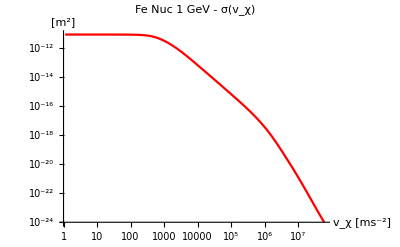

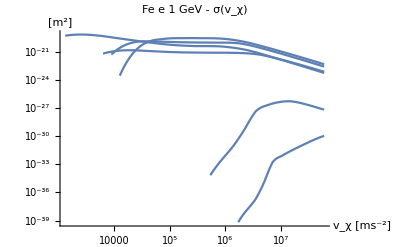

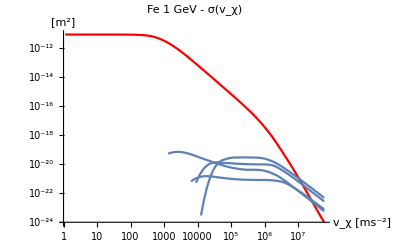

```mathematica
LogLogPlot[10^(#[Log10@vχ]),{vχ,10^(#["Domain"][[1,1]]),10^(#["Domain"][[1,2]])},PlotLabel->"Fe Nuc 1 GeV - σ(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^2]"},PlotStyle->Red]&@FeσDictNuc[[4]]["σf"]
Show[Table[LogLogPlot[10^(#[Log10@vχ]),{vχ,10^(#["Domain"][[1,1]]),10^(#["Domain"][[1,2]])},PlotLabel->"Fe e 1 GeV - σ(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^2]"},PlotRange->{{10^3,10^7},{10^-18,10^-40}}]&@FeσDicte[[4,i]]["σf"],{i,Length[FeσDicte[[4]]]}]]
Show[{%%,%},PlotLabel->"Fe 1 GeV - σ(v_χ)"]
```

Not surprisingly, we see that the per target cross-section is much higher for nuclear than for electronic for a slow moving aDM probe with a 1 GeV mass. In the electronic plot you can also see that the cross-sections for each “shell” cuts off as the incoming speed (and so maximum E_R) drop below some threshold. This corresponds roughly to an ionization energy for the “shell”. The “shell” with the lowest threshold corresponds to the conduction electrons. In principle the minimum E_R can be arbitrarily low, but once E_R < O(meV) phonons become important and our model breaks down, so we cutoff the cross-section rather than go down that rabbit hole (in the case of the silicates, which are insulators, this happens because we run into a band gap).

Note that each interpolation function comes with a list of keys (accessed by calling [“Methods”] on the interpolating function) that can be used to access information such as the domain of validity, or the points at which the function was evaluated etc. We used the domain method above when plotting.

```mathematica
(FeσDictNuc[[4]]["dσf"])["Methods"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

The prescription for summing cross-section across targets is to weight them by the target density. If this sum isn’t normalized this gives the inverse interaction length of the material (λ^-1). So for Iron we have for the interaction length (remembering to restrict each shell to it’s domain)

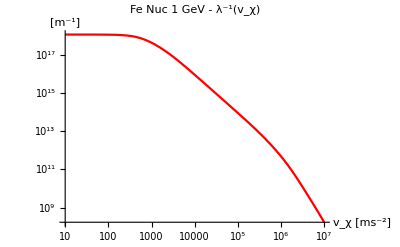

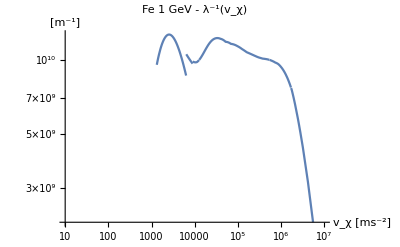

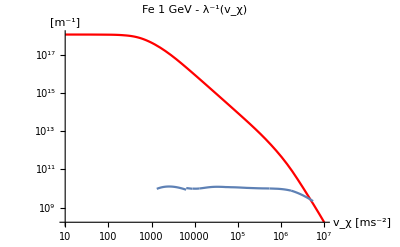

```mathematica
Quiet["nI"10^("σf"[Log10@#])Boole["σf"["Domain"][[1,1]]<Log10@#<"σf"["Domain"][[1,2]]]/.FeσDictNuc[[4]]/.FeσDictNuc[[4]]["NucleusParams"]]&(*[10^5]*);
Pnuc = Quiet@LogLogPlot[%@vχ,{vχ,10^1,10^7},PlotStyle->Red,PlotLabel->"Fe Nuc 1 GeV - λ^-1(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^-1]"}]
Quiet@Sum["ne"10^("σf"[Log10@#])Boole["σf"["Domain"][[1,1]]<Log10@#<"σf"["Domain"][[1,2]]]/.FeσDicte[[4,i]]/.FeσDicte[[4,i]]["params"],{i,Length[FeσDicte[[4]]]}]&;
Pe = Quiet@LogLogPlot[%@vχ,{vχ,10^1,10^7},PlotLabel->"Fe 1 GeV - λ^-1(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^-1]"}]
Show[{Pnuc,Pe},PlotLabel->"Fe 1 GeV - λ^-1(v_χ)"]
```

Note that the discontinuities in the electronic interaction length are physical and correspond to the aforementioned ionization thresholds.

As we might expect, since the cross-sections number density for nuclei and electrons is equal given that the materials are neutral, the previous plots of the cross-sections for the individual shells gives a good representation of the relative strengths of the total cross-sections summing over shells, and we again conclude that Nuclear scattering dominates the interaction length for aDM masses of order GeV.

For an MeV aDM

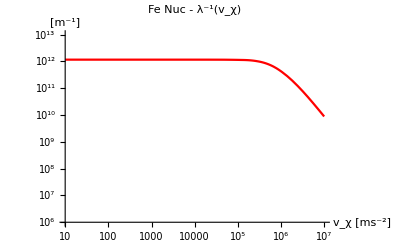

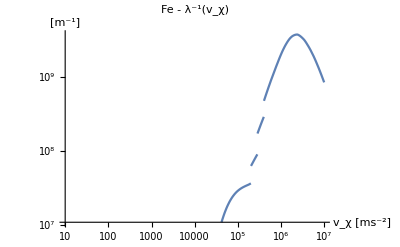

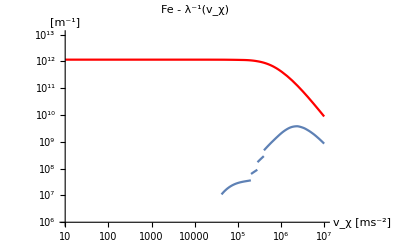

```mathematica
massind=Position[Round@Log10["mχ"(("JpereV")/("c")^2)^-1]/.FeσDictNuc/.SIConstRepl,Round@6][[1,1]];
Quiet["nI"10^("σf"[Log10@#])Boole["σf"["Domain"][[1,1]]<Log10@#<"σf"["Domain"][[1,2]]]/.FeσDictNuc[[1]]/.FeσDictNuc[[massind]]["NucleusParams"]]&(*[10^5]*);
Pnuc = Quiet@LogLogPlot[%@vχ,{vχ,10^1,10^7},PlotStyle->Red,PlotLabel->"Fe Nuc - λ^-1(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^-1]"},PlotRange->{10^6,10^13}]
Quiet@Sum["ne"10^("σf"[Log10@#])Boole["σf"["Domain"][[1,1]]<Log10@#<"σf"["Domain"][[1,2]]]/.FeσDicte[[massind,i]]/.FeσDicte[[massind,i]]["params"],{i,Length[FeσDicte[[massind]]]}]&;
Pe = Quiet@LogLogPlot[%@vχ,{vχ,10^1,10^7},PlotLabel->"Fe - λ^-1(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^-1]"}]
Show[{Pnuc,Pe},PlotLabel->"Fe - λ^-1(v_χ)"]
```

For a PeV mass aDM

-Graphics-

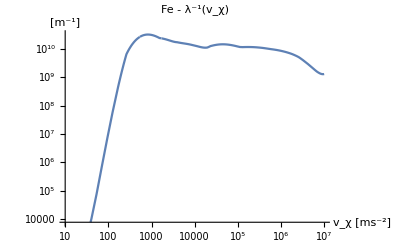

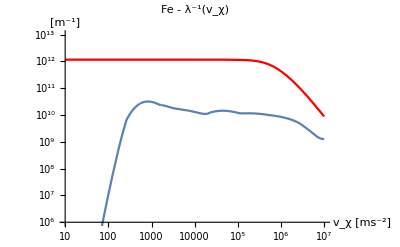

```mathematica
massind=Position[Round@Log10["mχ"(("JpereV")/("c")^2)^-1]/.FeσDictNuc/.SIConstRepl,Round@15][[1,1]];
Quiet["nI"10^("σf"[Log10@#])Boole["σf"["Domain"][[1,1]]<Log10@#<"σf"["Domain"][[1,2]]]/.FeσDictNuc[[1]]/.FeσDictNuc[[massind]]["NucleusParams"]]&(*[10^5]*);
Pnuc = Quiet@LogLogPlot[%@vχ,{vχ,10^1,10^7},PlotStyle->Red,PlotLabel->"Fe Nuc - λ^-1(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^-1]"},PlotRange->{10^6,10^13}]
Quiet@Sum["ne"10^("σf"[Log10@#])Boole["σf"["Domain"][[1,1]]<Log10@#<"σf"["Domain"][[1,2]]]/.FeσDicte[[massind,i]]/.FeσDicte[[massind,i]]["params"],{i,Length[FeσDicte[[massind]]]}]&;
Pe = Quiet@LogLogPlot[%@vχ,{vχ,10^1,10^7},PlotLabel->"Fe - λ^-1(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^-1]"}]
Show[{Pnuc,Pe},PlotLabel->"Fe - λ^-1(v_χ)"]
```